## Function library

```mathematica
(*Displacement shape functions*)Nu[ξ_,η_]:={(η ξ)/4-(η^2 ξ)/4-(η ξ^2)/4+(η^2 ξ^2)/4,-(η ξ)/4+(η^2 ξ)/4-(η ξ^2)/4+(η^2 ξ^2)/4,(η ξ)/4+(η^2 ξ)/4+(η ξ^2)/4+(η^2 ξ^2)/4,-(η ξ)/4-(η^2 ξ)/4+(η ξ^2)/4+(η^2 ξ^2)/4,-η/2+η^2/2+(η ξ^2)/2-(η^2 ξ^2)/2,ξ/2-(η^2 ξ)/2+ξ^2/2-(η^2 ξ^2)/2,η/2+η^2/2-(η ξ^2)/2-(η^2 ξ^2)/2,-ξ/2+(η^2 ξ)/2+ξ^2/2-(η^2 ξ^2)/2,1-η^2-ξ^2+η^2 ξ^2};
(*Pressure shape functions*)
Np[ξ_,η_]:={1/4-η/4-ξ/4+(η ξ)/4,1/4-η/4+ξ/4-(η ξ)/4,1/4+η/4+ξ/4+(η ξ)/4,1/4+η/4-ξ/4-(η ξ)/4};
(*Derivative of displacement shape functions w.r.t. ξ*)
dNdξ[ξ_,η_]:={η/4-η^2/4-(η ξ)/2+(η^2 ξ)/2,-η/4+η^2/4-(η ξ)/2+(η^2 ξ)/2,η/4+η^2/4+(η ξ)/2+(η^2 ξ)/2,-η/4-η^2/4+(η ξ)/2+(η^2 ξ)/2,η ξ-η^2 ξ,1/2-η^2/2+ξ-η^2 ξ,-η ξ-η^2 ξ,-1/2+η^2/2+ξ-η^2 ξ,-2 ξ+2 η^2 ξ};
(*Derivative of displacement shape functions w.r.t. η*)
dNdη[ξ_,η_]:={ξ/4-(η ξ)/2-ξ^2/4+(η ξ^2)/2,-ξ/4+(η ξ)/2-ξ^2/4+(η ξ^2)/2,ξ/4+(η ξ)/2+ξ^2/4+(η ξ^2)/2,-ξ/4-(η ξ)/2+ξ^2/4+(η ξ^2)/2,-1/2+η+ξ^2/2-η ξ^2,-η ξ-η ξ^2,1/2+η-ξ^2/2-η ξ^2,η ξ-η ξ^2,-2 η+2 η ξ^2};

(*Compute the B matrix and Det(J) for each element*)
computeBandJ[elemCoords_,ξ_,η_]:=Module[{X,Y,J11,J12,J21,J22,J11inv,J12inv,J21inv,J22inv,detJ,dNdξeval,dNdηeval,zeros,Nmat,Γ,Dmat,Bmat},

X=elemCoords⟦All,1⟧;
Y=elemCoords⟦All,2⟧;

dNdξeval =dNdξ[ξ,η];
dNdηeval =dNdη[ξ,η];

J11=X.dNdξeval;
J12=Y.dNdξeval;
J21=X.dNdηeval;
J22=Y.dNdηeval;

detJ=J11 J22 - J12 J21;

J11inv=J22 / detJ;
J12inv = -J12 / detJ;
J21inv = -J21 / detJ;
J22inv = J11 / detJ;

zeros=ConstantArray[0,Length[dNdξeval]];

Nmat={Riffle[dNdξeval,zeros],Riffle[dNdηeval,zeros],Riffle[zeros,dNdξeval],Riffle[zeros,dNdηeval]};

Γ={{J11inv,J12inv,0,0},
    {J21inv,J22inv,0,0},
    {0,0,J11inv,J12inv},
    {0,0,J21inv,J22inv}};

Dmat={{1,0,0,0},{0,0,0,1},{0,1,1,0}};

Bmat = Dmat.Γ.Nmat;

Return[{Bmat,detJ}];

]

(*Compute element ke and qe integrands*)
computeStiffnessAndQIntegrands[elemCoords_,ξ_,η_,μ_,ν_,α_]:=Module[{Ey,c11,c22,c12,c66,c21,Bmat,detJ,Cmat,Npeval,m},

Ey=2.0μ(1.0+ν);
c11=Ey(1.0-ν^2)/((1.0+ν)(1.0-ν-2.0 ν^2));
c12=Ey ν/(1.0-ν-2.0 ν^2);
c66=Ey/(2.0(1.0+ν));

Cmat={{c11,c12,0},{c12,c11,0},{0,0,c66}};

{Bmat,detJ}=computeBandJ[elemCoords,ξ,η];

m={1,1,0};
Npeval=Np[ξ,η];

Return[{Bmatᵀ.Cmat.Bmat detJ,α Outer[Times,Bmatᵀ.m, Npeval]detJ }]

];

(*Post processing function to compute stress*)
computeStessAtGaussPts[elemCoords_,disp_,μ_,ν_,α_]:=Module[{Ey,c11,c22,c12,c66,c21,points,Cmat,stress},

Ey=2.0μ(1.0+ν);
c11=Ey(1.0-ν^2)/((1.0+ν)(1.0-ν-2.0 ν^2));
c12=Ey ν/(1.0-ν-2.0 ν^2);
c66=Ey/(2.0(1.0+ν));

Cmat={{c11,c12,0},{c12,c11,0},{0,0,c66}};

points={-Sqrt[3/5.],0.0,Sqrt[3/5.]};

stress=Table[Cmat.(computeBandJ[elemCoords,points⟦i⟧,points⟦j⟧]⟦1⟧).Flatten[disp],{i,1,3},{j,1,3}];

Return[stress]

];

(*Post processing function to compute the coordinates of the Gauss points*)
computeGaussPtCoords[coords_]:=Module[{X,Y,points,gaussCoords},

X=coords⟦All,1⟧;
Y=coords⟦All,2⟧;

points={-Sqrt[3/5.],0.0,Sqrt[3/5.]};
gaussCoords=Table[{X.Nu[points⟦i⟧,points⟦j⟧],Y.Nu[points⟦i⟧,points⟦j⟧]},{i,1,3},{j,1,3}];

Return[gaussCoords]

]

(*Integrate ke and qe w/ 3 x 3 Gauss integration*)
computeElementStiffnessAndQ[elemCoords_,μ_,ν_,α_]:=Module[{weights,points,ke,qe},

weights={5/9., 8/9. ,5/9.};
points={-Sqrt[3/5.],0.0,Sqrt[3/5.]};

ke=ConstantArray[0.0,{18,18}];
qe=ConstantArray[0.0,{18,4}];

{ke,qe}= Sum[weights⟦i⟧ weights⟦j⟧ computeStiffnessAndQIntegrands[elemCoords,points⟦i⟧,points⟦j⟧,μ,ν,α],{i,1,3},{j,1,3}];

Return[{ke,qe}];

];

(*Create a DOF map for the global tangent stiffness*)
createDOFMap[connect_,numNodes_]:=Module[{dofMap,noPressureDOF,k},

(*Initialize 3 DOF for every node*)
dofMap=ConstantArray[{0,0,0},numNodes];
(*Find the nodes that do not have pressure DOF*)
noPressureDOF=Union[Flatten@connect[[All,5;;9]]];
(*Flag the pressure DOFs in the map on nodes that should not have a pressure DOF*)
dofMap[[noPressureDOF]]={0,0,-1};
dofMap=Flatten@dofMap;

(*Fill the non-flagged DOFs monotonically*)
k=1;
Do[
If[dofMap⟦i⟧==0,
dofMap⟦i⟧=k; k++
]
,{i,1,Length[dofMap]}
];

(*Delete the -1's, leaving a ragged array*)
dofMap =Select[#,#>0&]&/@Partition[dofMap,3];

Return[dofMap];
];

(*Assemble global tangent stiffness*)
assemble[coords_,connect_,μ_,ν_,α_]:=Module[{numNodes,dofMap,numDOF,globalK,elemCoords,qe,ke,dispDOF,presDOF},

numNodes=Length[coords];
dofMap=createDOFMap[connect,numNodes];

numDOF = Length[Flatten@dofMap];

globalK=ConstantArray[0.0,{numDOF,numDOF}];

Do[

elemCoords=coords⟦connect⟦i⟧⟧;

{ke,qe}=computeElementStiffnessAndQ[elemCoords,μ,ν,α];

dispDOF=Flatten@dofMap⟦connect⟦i⟧,1;;2⟧;
presDOF=Flatten@dofMap⟦connect⟦i,1;;4⟧,3⟧;

globalK⟦dispDOF,dispDOF⟧+=ke;
globalK⟦dispDOF,presDOF⟧+=qe;
globalK⟦presDOF,dispDOF⟧+=qeᵀ;

,{i,Length[connect]}
];

Return[globalK]
]
```

## Solution

Problem setup

```mathematica
(*Import the input files*)
coords=Import["http://johnfoster.pge.utexas.edu/PGE383-AdvGeomechanics/files/coords.csv"];
connect=Import["http://johnfoster.pge.utexas.edu/PGE383-AdvGeomechanics/files/connect.csv"];
nodeset1=Import["http://johnfoster.pge.utexas.edu/PGE383-AdvGeomechanics/files/nodeset1.csv"];
nodeset2=Import["http://johnfoster.pge.utexas.edu/PGE383-AdvGeomechanics/files/nodeset2.csv"];
nodeset3=Import["http://johnfoster.pge.utexas.edu/PGE383-AdvGeomechanics/files/nodeset3.csv"];
nodeset4=Import["http://johnfoster.pge.utexas.edu/PGE383-AdvGeomechanics/files/nodeset4.csv"];

(*Set material properties*)
α=1.0;
ν=.3;
μ=1.0;
```

Assembly

```mathematica
(*Assemble the global stiffness matrix*)
K= assemble[coords,connect,μ,ν,α];
```

```mathematica
(*Get the DOF map, this is the same one used in the assembly*)
dofMap=createDOFMap[connect,Length[coords]];
```

Boundary condition application

```mathematica
(*Fix y along horizontal*)
ns3Idx=dofMap⟦Flatten@nodeset3,2⟧;
Do[

K⟦i⟧=Normal@SparseArray[i-> 1,Length[K]]

,{i,ns3Idx}
]

(*Fix x along vertical*)
ns4Idx=dofMap⟦Flatten@nodeset4,1⟧;
Do[

K⟦i⟧=Normal@SparseArray[i-> 1,Length[K]]

,{i,ns4Idx}
]
```

```mathematica
(*Set pressure on interior*)
ns1Idx=dofMap[[Flatten@nodeset1]][[Flatten@Position[Length[#]&/@dofMap[[Flatten@nodeset1]],3],3]];
Do[

K⟦i⟧=Normal@SparseArray[i-> 1,Length[K]]

,{i,ns1Idx}
]

(*Allocate r.h.s vector and set interior pressure to 1*)
F=ConstantArray[0.0,Length[K]];
F⟦ns1Idx⟧=1.0;

(*Set far field pressure*)
ns2Idx=dofMap[[Flatten@nodeset2]][[Flatten@Position[Length[#]&/@dofMap[[Flatten@nodeset2]],3],3]];
Do[

K⟦i⟧=Normal@SparseArray[i-> 1,Length[K]]

,{i,ns2Idx}
]
```

Solve the linear problem

```mathematica
(*Solve problem*)
sol=LinearSolve[SparseArray[K],F];
```

```mathematica
(*Get displacments from solution vector*)
dispIdx=Flatten@dofMap⟦All,1;;2⟧;
displacements=Partition[sol⟦dispIdx⟧,2];

(*Set the deformed position*)
defPos=coords+displacements;
```

Create plots

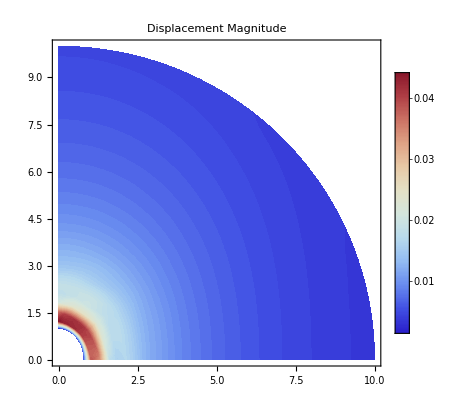

```mathematica
(*Compute the displacement magnitude*)
dispMag = Sqrt[displacements⟦All,1⟧^2+displacements⟦All,2⟧^2];

(*Plot the displacement magnitude*)
regionFun[{x_,y_}]:=1≤ Sqrt[x^2/0.8^2+y^2/1^2];
input={defPos⟦All,1⟧,defPos⟦All,2⟧,dispMag}ᵀ;
ListContourPlot[input,AspectRatio->1,InterpolationOrder->5,PlotLegends->Automatic,PlotRange-> {0,0.06},Contours-> 100,ContourStyle-> None,ColorFunction->"ThermometerColors",RegionFunction->Function[{x,y},regionFun[{x,y}]],PlotLabel->"Displacement Magnitude"]
```

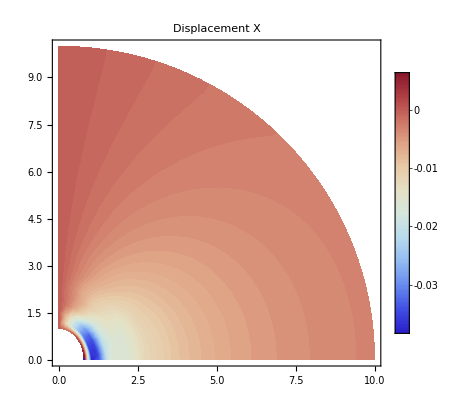

```mathematica
(*Plot the X displacement*)
input={defPos⟦All,1⟧,defPos⟦All,2⟧,displacements⟦All,1⟧}ᵀ;
ListContourPlot[input,AspectRatio->1,InterpolationOrder->5,PlotLegends->Automatic,PlotRange-> {-0.06,0.01},Contours-> 100,ContourStyle-> None,ColorFunction->"ThermometerColors",RegionFunction->Function[{x,y},regionFun[{x,y}]],PlotLabel->"Displacement X"]
```

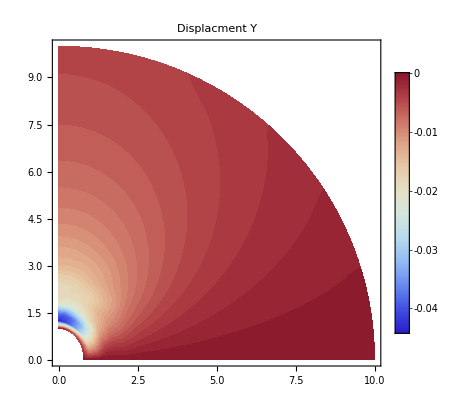

```mathematica
(*Plot the Y displacement*)
input={defPos⟦All,1⟧,defPos⟦All,2⟧,displacements⟦All,2⟧}ᵀ;
ListContourPlot[input,AspectRatio->1,InterpolationOrder->5,PlotLegends->Automatic,PlotRange-> {-0.08,0.03},Contours-> 100,ContourStyle-> None,ColorFunction->"ThermometerColors",RegionFunction->Function[{x,y},regionFun[{x,y}]],PlotLabel->"Displacment Y"]
```

```mathematica
(*Get the pressures DOF from the solution vector*)
presDOF=dofMap⟦Flatten@Position[Length[#]&/@dofMap,3]⟧⟦All,3⟧;
pressures=sol⟦presDOF⟧;
```

```mathematica
(*Get the displacement rows that have pressure DOFs*)
dispRowsThatHavePres=Flatten@Position[Length[#]&/@dofMap,3];
```

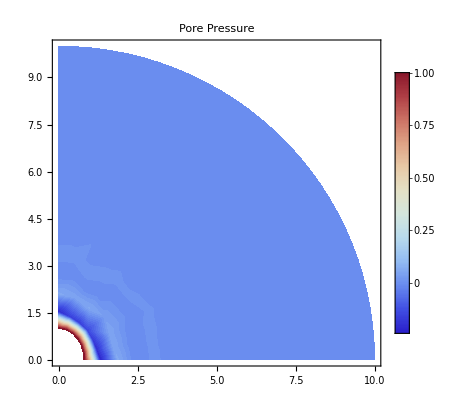

```mathematica
input={defPos⟦dispRowsThatHavePres,1⟧,defPos⟦dispRowsThatHavePres,2⟧,pressures}ᵀ;
ListContourPlot[input,AspectRatio->1,InterpolationOrder->5,PlotLegends->Automatic,PlotRange-> {-0.75,1},Contours-> 100,ContourStyle-> None,ColorFunction->"ThermometerColors",RegionFunction->Function[{x,y},regionFun[{x,y}]],PlotLabel->"Pore Pressure"]
```

```mathematica
stress=Partition[Flatten@Table[computeStessAtGaussPts[coords⟦connect⟦i⟧⟧,displacements⟦connect⟦i⟧⟧,μ,ν,α],{i,1,Length[connect]}],3];
gaussCoords=Partition[Flatten@Table[computeGaussPtCoords[coords⟦connect⟦i⟧⟧],{i,1,Length[connect]}],2];
```

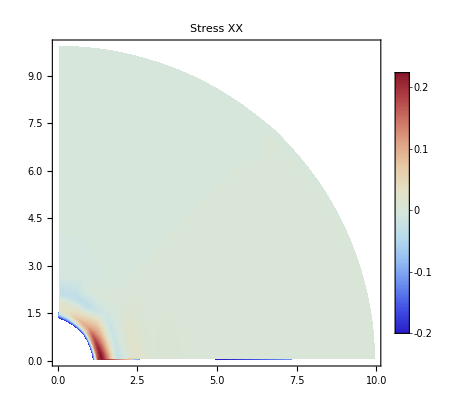

```mathematica
input={gaussCoords⟦All,1⟧,gaussCoords⟦All,2⟧,stress⟦All,1⟧}ᵀ;
ListContourPlot[input,AspectRatio->1,InterpolationOrder->5,PlotLegends->Automatic,Contours-> 100,ContourStyle-> None,ColorFunction->"ThermometerColors",RegionFunction->Function[{x,y},regionFun[{x,y}]],PlotLabel->"Stress XX",PlotRange->{-0.2,0.3}]
```

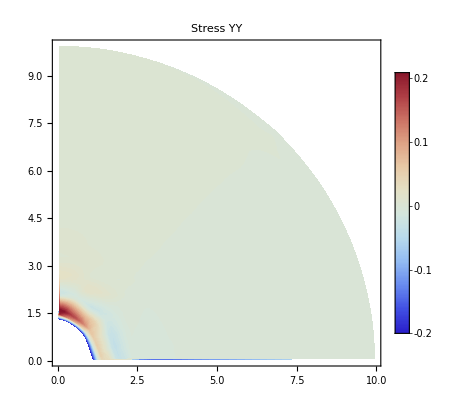

```mathematica
input={gaussCoords⟦All,1⟧,gaussCoords⟦All,2⟧,stress⟦All,2⟧}ᵀ;
ListContourPlot[input,AspectRatio->1,InterpolationOrder->5,PlotLegends->Automatic,Contours-> 100,ContourStyle-> None,ColorFunction->"ThermometerColors",RegionFunction->Function[{x,y},regionFun[{x,y}]],PlotLabel->"Stress YY",PlotRange->{-0.2,0.3}]
```

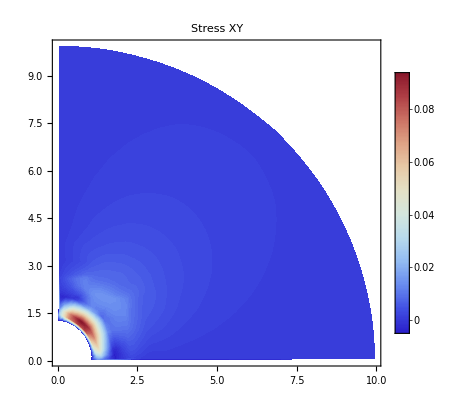

```mathematica
input={gaussCoords⟦All,1⟧,gaussCoords⟦All,2⟧,stress⟦All,3⟧}ᵀ;
ListContourPlot[input,AspectRatio->1,InterpolationOrder->5,PlotLegends->Automatic,Contours-> 100,ContourStyle-> None,ColorFunction->"ThermometerColors",RegionFunction->Function[{x,y},regionFun[{x,y}]],PlotLabel->"Stress XY",PlotRange->{-0.005,0.1}]
```